```mathematica
energies={}
```

{}

```mathematica
Distance=1;
Λ[x_]=0.3127477*x-0.0231669*x^2-0.0005110 x^3-0.0000045 x^4;
R=10
```

10

```mathematica
energies={};
For[i=1,i<=10,i+=1,
Distance=i;
minC=-20;
maxC=-0.5;
list={};
list2={};
step=0.001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g'[1.000001]==(c-Λ[c])/2},g,{ξ,1.000001,R}];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, temp[R]];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[int[x]==0,{x,-2}];
AppendTo[energies, 4*theC/Distance^2]
]
```

1

2

3

4

5

6

$Aborted

```mathematica
Distance=10;
minC=-30;
maxC=-10;
list={};
list2={};
step=0.001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g'[1.000001]==(c-Λ[c])/2},g,{ξ,1.000001,R}];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, temp[R]];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[int[x]==0,{x,minC}];
ListPlot[xy]
```

10

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

```mathematica
theC
```

-29.9571

```mathematica
4*theC/Distance^2
```

-1.19828

```mathematica
AppendTo[energies, 4*theC/Distance^2]
```

{-2.8873,-2.19609,-1.82044,-1.59401,-1.44978,-1.35604,-1.29489,-1.25401,-1.22381,-1.19828}

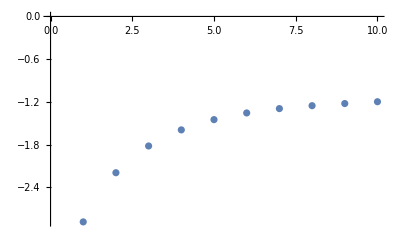

```mathematica
ListPlot[energies]
```

```mathematica
energiesL
```

{-2.8873,-2.19609,-0.636479,-0.148415,-0.282988}

```mathematica
energies
```

{-2.8873,-0.752666,-0.75082,-0.72714,-0.700161,-0.299138,-0.310106,-0.312176,-0.309909,-0.13308,-0.148415,-0.157912,-0.163512,0.0307946,-0.0605899,-0.0727978,-0.081994,-0.088882,-0.0939899,0.112774,-0.0265226,-0.0351448,-0.0422511,-0.0481073,-0.0529275,-2.8873,-0.718155,-0.312132,-0.148415,-0.0503219,-0.0868069,-0.0265226,-0.0498198,-0.00753585,-0.0253185,-2.8873,-0.718155,-0.312132,-0.148415,0.0561308,-0.0868069,-0.0265226,-0.0498198,-0.00753585,-0.0253185}

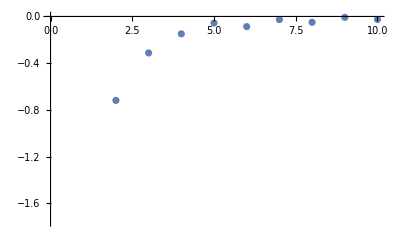

```mathematica
ListPlot[{-2.887297100948559,-0.7181546234953724,-0.3121319788770584,-0.14841452501477667,-0.056130750254556876,-0.08680691460231037,-0.026522601432019045,-0.04981982667323193,-0.007535849922041164,-0.02531847571115582}]
```

NDSolve::ndsz: At ξ == 1., step size is effectively zero; singularity or stiff system suspected.

{{g→InterpolatingFunction[…]}}

{InterpolatingFunction[…][ξ]}

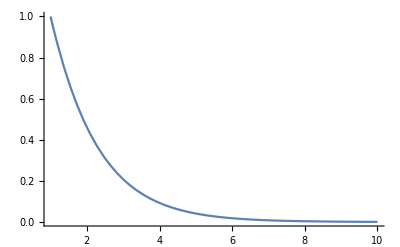

```mathematica
c=theC;
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g'[1.000001]==(c-Λ[c])/2},g,{ξ,1,R}]
r[ξ_]=g[ξ]/.sol
Plot[r[ξ]/.sol,{ξ,1.000001, R},PlotRange->All]
```

```mathematica
(*angular equation*)
Clear[f]
phiSol=NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[0.99999999]==1,f[-0.99999999]==1},f,{η,-0.99999999,0.99999999}]
```

{{f→InterpolatingFunction[…]}}

{InterpolatingFunction[…][η]}

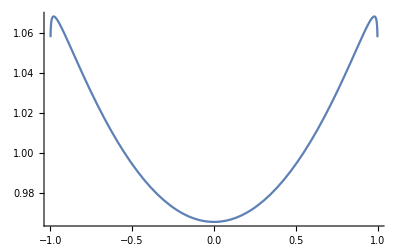

```mathematica
angSol[η_]=(f[η]/.phiSol)(1-η^2)^0
Plot[angSol[η],{η,-0.999,0.999},PlotRange->All]
```

```mathematica
NIntegrate[angSol[η]^2 r[ξ]^2 Distance^3/8(ξ^2-η^2),{ξ,1.000001,10},{η,-0.999999,0.999999}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.438032}

```mathematica
Energy=4*c/Distance^2
```

-2.8873

```mathematica
ra[x_,z_]=√((z+Distance/2)^2+x^2);
rb[x_,z_]=√((z-Distance/2)^2+x^2);
ξ[x_,z_]=(ra[x,z]+rb[x,z])/Distance;
η[x_,z_]=(ra[x,z]-rb[x,z])/Distance;
ψ[ξ_,η_]=r[ξ]*angSol[η]
Ψ1[x_,z_]=Piecewise[{{ψ[ξ[x,z],η[x,z]],x>0 && z>0},{ψ[ξ[-x,z],η[-x,z]],x<=0 && z>0},{ψ[ξ[x,-z],η[x,-z]],x>0&&z≤0},{ ψ[ξ[-x,-z],η[-x,-z]],x≤0&&z≤0}}];
```

{InterpolatingFunction[…][η] InterpolatingFunction[…][ξ]}

```mathematica
Plot3D[Ψ1[x,z],{x,-5,5},{z,-5,5},PlotRange->All]
```

-Graphics3D-